## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="ADK1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_ADK1";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(amp^c+atp^c⇌2 adp^c)^ADK1

Random Bi Bi; [adp, adp, atp || amp, adp || atp]

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | amp,Null;atp,Null | 1.97 | 1.8715
2.0685 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000105 | 0.00009975
0.00011025 |  | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | atp | 0.000046 | 0.0000437
0.0000483 | amp | 0.001 | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | amp | 0.000044 | 0.0000418
0.0000462 | atp | 0.001 | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null | 319 | 303.05
334.95 | 1/s | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | amp | Null
atp | Null | 1296 | 1231.2
1360.8 | 1/s | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(amp^c+atp^c⇌2 adp^c)^ADK1

Random Bi Bi; [adp, adp, atp || amp, adp || atp]

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | amp,Null;atp,Null | 1.97 | 1.8715
2.0685 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.000105 | 0.00009975
0.00011025 |  | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | atp | 0.000046 | 0.0000437
0.0000483 | amp | 0.001 | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | amp | 0.000044 | 0.0000418
0.0000462 | atp | 0.001 | M | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | Null | 319 | 303.05
334.95 | 1/s | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | amp | Null
atp | Null | 1296 | 1231.2
1360.8 | 1/s | 7.4 | 40 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_ADK1[c] + amp[c] <=> E_ADK1[c]&amp",
				"E_ADK1[c] + atp[c] <=> E_ADK1[c]&atp",

				"E_ADK1[c]&atp + amp[c] <=> E_ADK1[c]&atp&amp",
				"E_ADK1[c]&amp + atp[c] <=> E_ADK1[c]&atp&amp",

				"E_ADK1[c]&atp&amp <=> E_ADK1[c]&adp&adp",

				"E_ADK1[c]&adp&adp <=> E_ADK1[c]&adp + adp[c]",
				"E_ADK1[c]&adp <=> E_ADK1[c] + adp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((ADK1^c)_^+atp^c⇌(ADK1^c&atp^c)_^)^ADK11,((ADK1^c)_^+amp^c⇌(ADK1^c&amp^c)_^)^ADK12,((ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c)^ADK13,((ADK1^c&amp^c)_^+atp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK14,((ADK1^c&atp^c)_^+amp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK15,((ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c)^ADK16,((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((ADK1^c)_^+atp^c⇌(ADK1^c&atp^c)_^)^ADK11,Overscript[(ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c, ADK13],((ADK1^c&atp^c)_^+amp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK15,Overscript[(ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c, ADK16],((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17};
catalyticReactionsSet2={((ADK1^c)_^+amp^c⇌(ADK1^c&amp^c)_^)^ADK12,Overscript[(ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c, ADK13],((ADK1^c&amp^c)_^+atp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK14,Overscript[(ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c, ADK16],((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2}
```

{{((ADK1^c)_^+atp^c⇌(ADK1^c&atp^c)_^)^ADK11,((ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c)^ADK13,((ADK1^c&atp^c)_^+amp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK15,((ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c)^ADK16,((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17},{((ADK1^c)_^+amp^c⇌(ADK1^c&amp^c)_^)^ADK12,((ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c)^ADK13,((ADK1^c&amp^c)_^+atp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK14,((ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c)^ADK16,((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17}}

### Setup King-Altman Equations

```mathematica
Get["MASSef`"]
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

{amp^c→0,atp^c→0}

{adp^c→0}

{amp^c→∞,atp^c→∞}

{adp^c→∞}

{((ADK1^c&atp^c&amp^c)_^-((ADK1^c&adp^c&adp^c)_^)/K_ADK17) Volume_c k_ADK17^⟶}

1

2

3

1.12585

4

0.00227

5

0.00034

6

0.000764

kcat for

kcat rev

km for

km rev

repeated met: adp

otherMetsReverseZeroSub

otherMetsForwardZeroSub

OI

***

5

5

5

***

```mathematica
forwardZeroSub={amp^c->0,atp^c->0};
eqRateConstSub={};
```

#### ADK1 Specific Work-Around for Double Substrate Binding Effects

```mathematica
symbolicKmReverse=Solve[((absoluteFlux[[2]]/.eqRateConstSub)/.forwardZeroSub/.eqRateConstSub)== Limit[((absoluteFlux[[2]]/.eqRateConstSub)/.forwardZeroSub/.eqRateConstSub),adp^c-> ∞]/2,adp^c];
relativeRateReverseBla=Simplify[symbolicKmReverse[[1,1,2]](*/.haldaneSub/.eqRateConstSub*)];
```

```mathematica
(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Get["MASSef`"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.127151,0.127151,0.127151}

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	amp[c]	atp[c]	param_ADK1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt"	1.97
1	0.000010500000000000005	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.000016641378520841707	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.000026374807530850625	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.000041801252908117194	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.0000662505211704203	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.00010500000000000005	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.00016641378520841705	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.00026374807530850624	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.00041801252908117237	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.000662505211704203	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0.0010500000000000006	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt"	0.000105
1	0	0.001	4.6000000000000025e-6	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.09090909090909097
1	0	0.001	7.290508685321129e-6	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.1368068886032101
1	0	0.001	0.000011554677584944084	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.20076000891310194
1	0	0.001	0.00001831292984546087	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.28474724895080133
1	0	0.001	0.000029024037846088895	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.386863179846857
1	0	0.001	0.00004600000000000003	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.5000000000000001
1	0	0.001	0.00007290508685321129	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.6131368201531432
1	0	0.001	0.00011554677584944084	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.7152527510491989
1	0	0.001	0.00018312929845460887	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.7992399910868985
1	0	0.001	0.0002902403784608889	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.8631931113967901
1	0	0.001	0.00046000000000000023	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt"	0.9090909090909091
1	0	4.399999999999995e-6	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.09090909090909081
1	0	6.973530046828895e-6	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.13680688860320994
1	0	0.00001105230029864215	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.20076000891310172
1	0	0.000017516715504353882	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.28474724895080145
1	0	0.000027762123157128463	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.3868631798468566
1	0	0.00004399999999999995	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.4999999999999998
1	0	0.00006973530046828894	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.6131368201531429
1	0	0.0001105230029864215	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.7152527510491986
1	0	0.00017516715504353863	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.7992399910868981
1	0	0.00027762123157128464	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.8631931113967899
1	0	0.00043999999999999953	0.001	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt"	0.9090909090909091
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0.01	0	0	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt"	319
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296
1	0	0.01	0.01	1	7.4	40	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt"	1296

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.05898881029
best_fit: 1.04188149502
best_fit: 1.04900274667
best_fit: 1.08498719943
best_fit: 1.09966951123

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat⟦2⟧ is longer than depth of object.

```mathematica
lmaResultsFileNew
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/output/raw/lmaResults_GAPD_20175241235.txt

```mathematica
Get["MASSef`"];
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_1 | 7.08841×10^-9 | 5.02455×10^-17 | 3.21537×10^-8 | 1.63217×10^-6 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | haldaneRatio_2 | 8.63854×10^-8 | 7.46244×10^-15 | 3.91852×10^-7 | 0.000019891 | 1.97 | 1.97
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateRev_adp | 0.0779108 | 0.00607009 | 0.000020632 | 19.6495 | 0.000105 | 0.000125632
1 | relRateFor_atp | 0.0000439345 | 1.93024×10^-9 | 9.19616×10^-6 | 0.0101158 | 0.0909091 | 0.0908999
1 | relRateFor_atp | 0.0000372981 | 1.39115×10^-9 | 0.0000117487 | 0.00858783 | 0.136807 | 0.136795
1 | relRateFor_atp | 0.0000287595 | 8.27108×10^-10 | 0.0000132941 | 0.0066219 | 0.20076 | 0.200747
1 | relRateFor_atp | 0.0000188284 | 3.54509×10^-10 | 0.0000123447 | 0.00433531 | 0.284747 | 0.284735
1 | relRateFor_atp | 8.77523×10^-6 | 7.70046×10^-11 | 7.81676×10^-6 | 0.00202055 | 0.386863 | 0.386855
1 | relRateFor_atp | 3.23884×10^-7 | 1.04901×10^-13 | 3.72885×10^-7 | 0.0000745771 | 0.5 | 0.5
1 | relRateFor_atp | 5.18618×10^-6 | 2.68965×10^-11 | 7.3219×10^-6 | 0.00119417 | 0.613137 | 0.613144
1 | relRateFor_atp | 7.52824×10^-6 | 5.66744×10^-11 | 0.0000123986 | 0.00173346 | 0.715253 | 0.715265
1 | relRateFor_atp | 7.51128×10^-6 | 5.64193×10^-11 | 0.0000138233 | 0.00172955 | 0.79924 | 0.799254
1 | relRateFor_atp | 6.28388×10^-6 | 3.94872×10^-11 | 0.0000124898 | 0.00144693 | 0.863193 | 0.863206
1 | relRateFor_atp | 4.73942×10^-6 | 2.24621×10^-11 | 9.92089×10^-6 | 0.0010913 | 0.909091 | 0.909101
1 | relRateFor_amp | 5.52278×10^-6 | 3.05011×10^-11 | 1.15607×10^-6 | 0.00127168 | 0.0909091 | 0.0909102
1 | relRateFor_amp | 5.04543×10^-6 | 2.54564×10^-11 | 1.58937×10^-6 | 0.00116176 | 0.136807 | 0.136808
1 | relRateFor_amp | 4.38031×10^-6 | 1.91871×10^-11 | 2.02488×10^-6 | 0.00100861 | 0.20076 | 0.200762
1 | relRateFor_amp | 3.50686×10^-6 | 1.2298×10^-11 | 2.2993×10^-6 | 0.000807487 | 0.284747 | 0.28475
1 | relRateFor_amp | 2.44492×10^-6 | 5.97764×10^-12 | 2.17791×10^-6 | 0.000562965 | 0.386863 | 0.386865
1 | relRateFor_amp | 1.26848×10^-6 | 1.60905×10^-12 | 1.4604×10^-6 | 0.00029208 | 0.5 | 0.500001
1 | relRateFor_amp | 9.2257×10^-8 | 8.51135×10^-15 | 1.30248×10^-7 | 0.000021243 | 0.613137 | 0.613137
1 | relRateFor_amp | 9.69011×10^-7 | 9.38983×10^-13 | 1.59589×10^-6 | 0.000223123 | 0.715253 | 0.715251
1 | relRateFor_amp | 1.8412×10^-6 | 3.39002×10^-12 | 3.38839×10^-6 | 0.000423951 | 0.79924 | 0.799237
1 | relRateFor_amp | 2.50419×10^-6 | 6.27098×10^-12 | 4.97726×10^-6 | 0.00057661 | 0.863193 | 0.863188
1 | relRateFor_amp | 2.9781×10^-6 | 8.86909×10^-12 | 6.23392×10^-6 | 0.000685731 | 0.909091 | 0.909085
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateRev | 3.63424×10^-10 | 1.32077×10^-19 | 2.66944×10^-7 | 8.36814×10^-8 | 319 | 319.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.
1 | absRateFor | 1.94942×10^-11 | 3.80023×10^-22 | 5.81751×10^-8 | 4.48882×10^-9 | 1296 | 1296.

### Simulated Data and Best Fit Data Plot

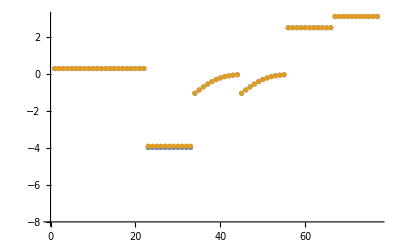

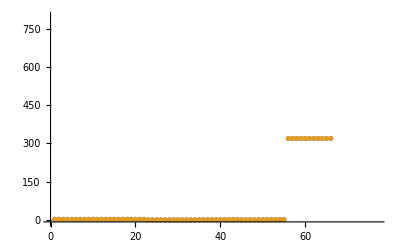

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10